```mathematica
SetDirectory[NotebookDirectory[]];
colorMap = 97;
cm = 72/2.54;

Needs["DatabaseLink`"];
Needs["JLink`"];
<<"helpers-data.wls";
<<"helpers-plot.wls";
```

```mathematica
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx4096m"];
conn = OpenSQLConnection[JDBC["PostgreSQL","teodor-desktop/teodor"],"Username"->"teodor", "Password"-> "4HWZQ3y60gKKcTNp"];
```

```mathematica
records = extractDataSet[conn, 232];
```

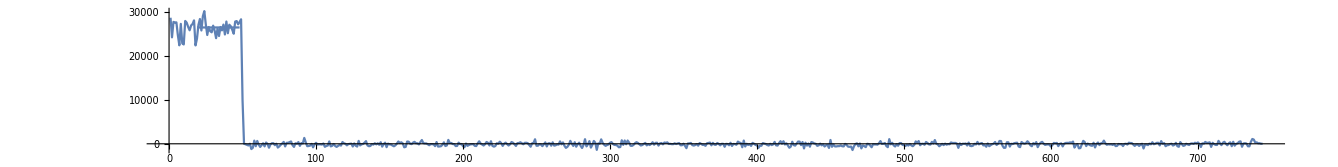

```mathematica
Show[
Prepend[
plotLevels[#],
ListLinePlot[#[[dataIntI, All, 2]],PlotRange->All]
],
AspectRatio->1/8,
ImageSize->30cm
]&@records[[2]]
```

```mathematica
data= Table[RandomReal[NormalDistribution[0, 1], {100, 100}], 100];
```